```mathematica
Reduce[n!/((n-4)!4!)≤ 100 && n > 4 && n < 10, {n},Integers]
```

$Aborted

```mathematica
FuncX[i] := Sum[Floor[2x/3],{x,1,5}]
```

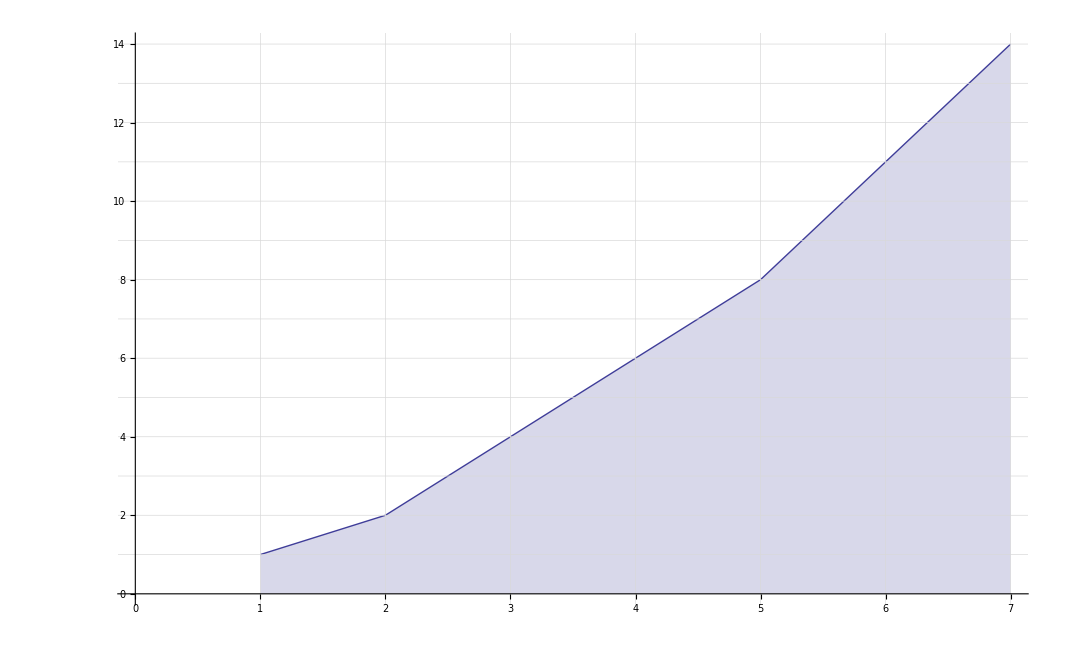

```mathematica
ListPlot[Table[Sum[x,{x,1,i}]-(Sum[Floor[2x/3],{x,1,i}]-Floor[i/3]), {i,1,7}], 
Joined->True, Filling->Automatic, PlotRange->{Automatic,Automatic}, GridLines->{Table[i,{i,1,10}],Table[i,{i,1,60}]}]
```

```mathematica
Table[Sum[x,{x,1,i}]-(Sum[Floor[2x/3],{x,1,i}]-Floor[i/3]), {i,1,10}]
```

{1,2,4,6,8,11,14,17,21,25}

```mathematica
Block[{j}, j=2;Table[Sum[Floor[2x/(2j)],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)]), {i,1,10}]]
```

{0,1,1,2,3,4,5,6,7,9}

```mathematica
Table[Sum[Floor[2x/2j],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)]), {i,1,10}]
```

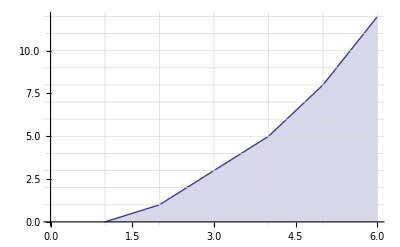

```mathematica
ListPlot[Table[Sum[Floor[2x/3],{x,1,i}], {i,1,6}], 
Joined->True, Filling->Automatic, PlotRange->{Automatic,Automatic}, GridLines->{Table[i,{i,1,10}],Table[i,{i,1,60}]}]
```

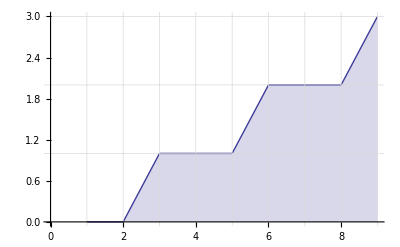

```mathematica
ListPlot[Table[Floor[x/3], {x,1,9}], 
Joined->True, Filling->Automatic, PlotRange->{Automatic,Automatic}, GridLines->{Table[i,{i,1,10}],Table[i,{i,1,60}]}]
```

```mathematica
Accumulate[Table[Sum[x,{x,1,i}]-(Sum[Floor[2x/3],{x,1,i}]+Floor[2i/3]), {i,1,10}]]
```

{1,2,3,6,10,15,23,33,45,61}

```mathematica
Table[Simplify[Sum[Floor[2x/(2j)],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)]), i ≥ 1 && Element[i,Integers] && OddQ[i] ], {j,1,100}]
```

Simplify::fas: Warning: One or more assumptions evaluated to False.

General::stop: Further output of Simplify will be suppressed during this calculation.

{1/6 (-6+5 i+3 i^2),1/5 (5+i-5 True),i/7,i/9,i/11,i/13,i/15,i/17,i/19,i/21}

```mathematica
ListPlot[Table [Simplify[Table[Sum[Floor[2x/(2j)],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)]) , {j,1,100}]i ≥ 1 && Element[i,Integers] && OddQ[i]], {i,1,1000,2}], Joined->True]
```

$Aborted

```mathematica
Table [Simplify[Table[Sum[Floor[2x/(2j)],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)]) , {j,1,i}],i ≥ 1 && Element[i,Integers] && OddQ[i]], {i,1,10,2}]
```

{{1},{4,1,1},{8,3,1,1,1},{14,5,3,1,1,1,1},{21,7,4,3,1,1,1,1,1}}

```mathematica
Sum[Floor[2x/(2j)],{x,1,i}]-(Sum[Floor[2x/(2j+1)],{x,1,i}]-Floor[i/(2j+1)])
```

```mathematica
Assuming[
i ≥ 1 && Element[i,Integers]  &&
j ≥ 1 && Element[j,Integers]&&
x ≥ 1 && Element[x,Integers],
FullSimplify[Floor[i/(1+2 j)]+∑_(x=1)^i Floor[x/j]-∑_(x=1)^i Floor[(2 x)/(1+2 j)]]
]
```

$Aborted